```mathematica
<<ECPack.wl
```

ECPack loaded: 91 commands.
Copyright (c) 2026, by B. Ananthanarayan, Darsh R. Bhatt and Parastoo Taghizadeh Asl

ECPack comes with ABSOLUTELY NO WARRANTY.
This is free software, and you are welcome to redistribute it under the terms of the GNU Public Licence. For assistance consult Darsh R. Bhatt @ darshbhatt.ssa@gmail.com
  ?ECP*  lists every command.

```mathematica
(*These examples were executed using Mathematica 13.2.In case you run the examples using higher versions of Mathematica,you might see some native Mathematica warnings that do not indicate the output is incorrect.*)
```

# Elliptic Curves, Modular Forms and their L-functions, Álvaro Lozano-Robledo

## Chapter 1: Introduction

### Example 1.1.3.

The curve E : y^2 = x^3 − 25x has a point (−4, 6). But E has other points, such as ( 1681/144 , 62279/1728 ).

```mathematica
ECPPointQ[ {-4,6},{-25,0}]
```

True

```mathematica
ECPPointQ[{1681/144, 62279/1728},{-25,0}]
```

True

```mathematica
A=-25;B=0;
P={-4,6};
ECPMultiply[2,P,{A,B}]
```

{1681/144,-62279/1728}

```mathematica
ECPJInvariant[{-25,0}]
```

1728

```mathematica
ECPShortWeierstrassForm[{-25,0}]
```

32400 x-x^3+y^2

```mathematica
ECPTorsionSubgroup[{-25,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-5,0}},Points→{∞,{-5,0},{0,0},{5,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-25,0}]
```

<|Rank→1,Parity→-1,Conductor→800|>

```mathematica
ECPFindGenerators[{-25,0}]
```

<|Rank→1,Generators→{{-4,-6}},Torsion→{∞,{-5,0},{0,0},{5,0}},RankBound→2,Curve→{-25,0},HeightMatrix→{{0.949743}},Determinant→0.949743,Time→25.1488|>

```mathematica
ECPIsMinimalShort[{-25,0}]
```

True

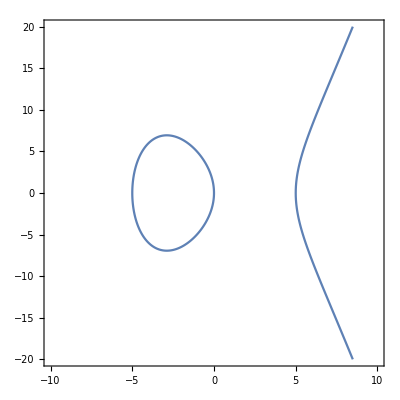

```mathematica
ContourPlot[y^2-(x^3-25 x)==0,{x,-10,10},{y,-20,20},PlotPoints->100,AspectRatio->1]
```

## Chapter 2: Elliptic Curves

### Example 2.2.3.

Let d ∈ Z, d ≠ 0 and let E be the elliptic curve given by the cubic equation: X^3 + Y^3 = dZ^3 with O = [1, −1, 0].

X^3+Y^3=dZ^3, Let d ∈ Z, d ≠ 0

Let d=10 :

```mathematica
F=x^3+y^3-10 z^3;
P={1,−1,0};

ECPCubicToWeierstrass[P, F]
```

2700-x^3+90 y+y^2

```mathematica
ECPJInvariant[{0,0,90,0,-2700}]
```

0

```mathematica
ECPShortWeierstrassForm[{0,0,90,0,-2700}]
```

31492800-x^3+y^2

```mathematica
ECPJInvariant[{0,-31492800}]
```

0

```mathematica
ECPJInvariant[{0,43200}]
```

0

ECPack yields the same j-invariant for all these curves. Therefore, they are all isomorphic.

```mathematica
ECPTorsionSubgroup[{0,0,90,0,-2700}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,90,0,-2700}]
```

<|Rank→0,Parity→1,Conductor→2700|>

```mathematica
ECPFindGenerators[{0,0,90,0,-2700}]
```

<|Rank→0,Generators→{},Torsion→{∞},RankBound→3,Curve→{0,0,90,0,-2700},HeightMatrix→{},Determinant→0,Time→0.00403881|>

### Example 2.3.1.

Let E be given by y^2 = x^3 + x/2 + 5/3 . We may change variables by x =X/6^2 and y =Y/6^3 to obtain a new equation Y^2= X^3 + 648X + 77760 with integral coefficients.

```mathematica
ECPWeierstrassDiscriminant[{0,0,0,1/2,5/3}]
```

-1208

```mathematica
ECPShortWeierstrassForm[{0,0,0,1/2,5/3}]
```

-77760-648 x-x^3+y^2

```mathematica
ECPWeierstrassDiscriminant[{648,77760}]
```

-2629553061888

```mathematica
ECPJInvariant[{0,0,0,1/2,5/3}]
```

1728/151

```mathematica
ECPJInvariant[{648,77760}]
```

1728/151

### Example 2.3.3.

Let E be the elliptic curve y^2 = x^3 − 25x. The points P = (5, 0) and Q = (−4, 6) belong to E(Q). Let us find P + Q and 2Q.

```mathematica
Q={-4,6};
P={5,0};
ECPAdd[P,Q,{-25, 0}]
```

{-5/9,-100/27}

```mathematica
ECPMultiply[2,Q,{-25,0}]
```

{1681/144,-62279/1728}

### Example 2.3.4.

Let E : y^2 = x^3+ 1 and put P = (2, 3). Let us find P , 2P , 3P , etc:

```mathematica
Table[ECPMultiply[n,{2,3},{0,1}],{n,{1,2,3,4,5,6}}]
```

{{2,3},{0,1},{-1,0},{0,-1},{2,-3},∞}

```mathematica
ECPTorsionSubgroup[{0,1}]
```

<|Order→6,Structure→Z/6Z,Generators→{{2,-3}},Points→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,1}]
```

<|Rank→0,Parity→1,Conductor→36|>

```mathematica
ECPFindGenerators[{0,1}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}},RankBound→2,Curve→{0,1},HeightMatrix→{},Determinant→0,Time→0.00327921|>

```mathematica
ECPJInvariant[{0,1}]
```

0

```mathematica
ECPShortDiscriminant[{0,1}]
```

-432

### Example 2.3.7.

(1) The curve E_1/Q : y^2 = x^3 + 6 has no rational points, other than the point at infinity O. Therefore, there are no torsion points (other than O) and no points of infinite order. In particular, the rank is 0, and E_1(Q) = {O}.

```mathematica
ECPTorsionSubgroup[{0,6}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,6}]
```

<|Rank→0,Parity→1,Conductor→15552|>

```mathematica
ECPFindGenerators[{0,0,0,0,6}]
```

<|Rank→0,Generators→{},Torsion→{∞},RankBound→2,Curve→{0,0,0,0,6},HeightMatrix→{},Determinant→0,Time→0.00264597|>

```mathematica
ECPJInvariant[{0,6}]
```

0

```mathematica
ECPShortDiscriminant[{0,6}]
```

-15552

```mathematica
ECPIsMinimal[{0,6}]
```

True

(2) The curve E_2/Q : y^2 = x^3 + 1 has only 6 rational points. The point P = (2, 3) has exact order 6. Therefore E_2(Q)≅Z/6Z is an isomorphism of groups. Since there are no points of infinite order, the rank of E_2/Q is 0, and E_2(Q) = {O, P, 2P, 3P, 4P, 5P } = {O, (2, ±3), (0, ±1), (−1, 0)}.

```mathematica
ECPFindPointOrder[{2,3},{0,1}]
```

6

```mathematica
ECPTorsionSubgroup[{0,1}]
```

<|Order→6,Structure→Z/6Z,Generators→{{2,-3}},Points→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,1}]
```

<|Rank→0,Parity→1,Conductor→36|>

```mathematica
ECPFindGenerators[{0,1}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}},RankBound→2,Curve→{0,1},HeightMatrix→{},Determinant→0,Time→0.0033927|>

(3) The curve E_3/Q : y^2 = x^3 − 2 does not have any rational torsion points other than O. However, the point P = (3, 5) is a rational point. Thus, P must be a point of infinite order and E_3(Q) contains infinitely many distinct rational points. In fact, the rank of E_3 is equal to 1 and P is a generator of all of E_3(Q).

```mathematica
ECPTorsionSubgroup[{0,-2}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPFindPointOrder[{3,5},{0,-2}]
```

∞

```mathematica
ECPAnalyticRank[{0,0,0,0,-2}]
```

<|Rank→1,Parity→-1,Conductor→1728|>

```mathematica
ECPFindGenerators[{0,-2}]
```

<|Rank→1,Generators→{{3,-5}},Torsion→{∞},RankBound→2,Curve→{0,-2},HeightMatrix→{{0.674789}},Determinant→0.674789,Time→2.02859|>

```mathematica
ECPJInvariant[{0,-2}]
```

0

```mathematica
ECPShortDiscriminant[{0,-2}]
```

-1728

```mathematica
ECPIsMinimalShort[{0,-2}]
```

True

(4) The elliptic curve E_4/Q : y^2 = x^3 + 7105 x^2 + 1327104x, features both torsion and infinite order points. In fact,
E_4 (Q) ≅ Z/4Z ⊕ Z^3. The torsion subgroup is generated by the point T = (1152, 111744) of order 4. The free part is generated by three points of infinite order:
P_1= (−6912, 6912), P_2 = (−5832, 188568), P_3 = (−5400, 206280).

```mathematica
ECPJInvariant[{0,7105,0,1327104,0}]
```

100542763314240451860097/310774320489037824

```mathematica
ECPWeierstrassDiscriminant[{0,7105,0,1327104,0}]
```

1272931616723098927104

```mathematica
ECPShortWeierstrassForm[{0,7105,0,1327104,0}]
```

-1092914553548160+20087876016 x-x^3+y^2

```mathematica
ECPTorsionSubgroup[{0,7105,0,1327104,0}]
```

<|Order→4,Structure→Z/4Z,Generators→{{1152,-111744}},Points→{∞,{0,0},{1152,-111744},{1152,111744}}|>

```mathematica
ECPAnalyticRank[{0,7105,0,1327104,0}]
```

<|Rank→3,Parity→-1,Conductor→2794182|>

```mathematica
ECPFindGenerators[{0,7105,0,1327104,0},"SearchBound"->250000]
```

<|Rank→3,Generators→{{-2304,-149760},{-1176,-81480},{-400,-23280}},Torsion→{∞,{0,0},{1152,-111744},{1152,111744}},RankBound→4,Curve→{0,7105,0,1327104,0},HeightMatrix→{{1.09052,0.457036,-0.281458},{0.457036,1.23477,-0.439982},{-0.281458,-0.439982,1.1828}},Determinant→1.14989,Time→975.276|>

### Example 2.4.1.

The curve y^2= x^3-n^2 x has three obvious rational points, namely P = (0, 0), Q = (-n, 0), T = (n, 0), and we will show that each of these three points is torsion of order 2.
Let n = 1,

```mathematica
ECPFindPointOrder[{0,0},{-1,0},10]
```

2

```mathematica
ECPFindPointOrder[{-1,0},{-1,0},10]
```

2

```mathematica
ECPFindPointOrder[{1,0},{-1,0},10]
```

2

```mathematica
ECPTorsionSubgroup[{-1,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-1,0}},Points→{∞,{-1,0},{0,0},{1,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-1,0}]
```

<|Rank→0,Parity→1,Conductor→32|>

```mathematica
ECPFindGenerators[{-1,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,0},{1,0}},RankBound→1,Curve→{-1,0},HeightMatrix→{},Determinant→0,Time→0.00320101|>

```mathematica
ECPJInvariant[{-1,0}]
```

1728

```mathematica
ECPShortDiscriminant[{-1,0}]
```

64

### Example 2.4.3.

The torsion subgroup of the elliptic curve with Weierstrass equation y^2 + 43xy − 210y = x^3 − 210 x^2 is isomorphic to Z/12Z and it is generated by the point (0, 210). The elliptic curve y^2 + 17xy − 120y = x^3 − 60 x^2 has a torsion subgroup
isomorphic to Z/2Z⊕Z/8Z, generated by the rational points (30, −90) and (−40, 400).

```mathematica
ECPShortWeierstrassForm[{43,-210,-210,0,0}]
```

-73697852646+33339627 x-x^3+y^2

```mathematica
ECPTorsionSubgroup[{43,-210,-210,0,0}]
```

<|Order→12,Structure→Z/12Z,Generators→{{-210,2940}},Points→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}}|>

```mathematica
ECPAnalyticRank[{43,-210,-210,0,0}]
```

<|Rank→0,Parity→1,Conductor→2730|>

```mathematica
ECPFindGenerators[{43,-210,-210,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}},RankBound→4,Curve→{43,-210,-210,0,0},HeightMatrix→{},Determinant→0,Time→0.199059|>

```mathematica
ECPJInvariant[{43,-210,-210,0,0}]
```

1882742462388824401/11650189824000

```mathematica
ECPWeierstrassDiscriminant[{43,-210,-210,0,0}]
```

11650189824000

```mathematica
ECPShortWeierstrassForm[{17,-60,-210,0,0}]
```

-860799366+2378187 x-x^3+y^2

```mathematica
ECPTorsionSubgroup[{17,-60,-120,0,0}]
```

<|Order→16,Structure→Z/2Z x Z/8Z,Generators→{{-40,400},{-30,180}},Points→{∞,{-40,400},{-30,180},{-30,450},{-12,36},{-12,288},{0,0},{0,120},{15/4,225/8},{24,-144},{30,-300},{30,-90},{60,-900},{60,0},{240,-5760},{240,1800}}|>

```mathematica
ECPAnalyticRank[{17,-60,-210,0,0}]
```

<|Rank→2,Parity→1,Conductor→13143270|>

```mathematica
ECPFindGenerators[{17,-60,-210,0,0},"SearchBound"->300]
```

<|Rank→2,Generators→{{0,0},{15/4,45/8}},Torsion→{∞},RankBound→4,Curve→{17,-60,-210,0,0},HeightMatrix→{{0.211324,-0.247358},{-0.247358,1.45709}},Determinant→0.246733,Time→11.1665|>

```mathematica
ECPJInvariant[{17,-60,-210,0,0}]
```

1992290159287/724221000

```mathematica
ECPWeierstrassDiscriminant[{17,-60,-210,0,0}]
```

248407803000

### Table - Page 32

Examples of each of the possible torsion subgroups over Q : 
-Graphics-;

Examples of each of the possible torsion subgroups over Q.

y^2=x^3−2

```mathematica
ECPTorsionSubgroup[{0,-2}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,-2}]
```

<|Rank→1,Parity→-1,Conductor→1728|>

```mathematica
ECPFindGenerators[{0,-2}]
```

<|Rank→1,Generators→{{3,-5}},Torsion→{∞},RankBound→2,Curve→{0,-2},HeightMatrix→{{0.674789}},Determinant→0.674789,Time→2.07274|>

```mathematica
ECPJInvariant[{0,-2}]
```

0

```mathematica
ECPWeierstrassDiscriminant[{0,-2}]
```

-1728

y^2 = x^3 + 8

```mathematica
ECPTorsionSubgroup[{0,8}]
```

<|Order→2,Structure→Z/2Z,Generators→{{-2,0}},Points→{∞,{-2,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,8}]
```

<|Rank→1,Parity→-1,Conductor→576|>

```mathematica
ECPFindGenerators[{0,8}]
```

<|Rank→1,Generators→{{1,-3}},Torsion→{∞,{-2,0}},RankBound→2,Curve→{0,8},HeightMatrix→{{0.326622}},Determinant→0.326622,Time→15.6587|>

```mathematica
ECPJInvariant[{0,8}]
```

0

```mathematica
ECPWeierstrassDiscriminant[{0,8}]
```

-27648

y^2 = x^3 + 4

```mathematica
ECPTorsionSubgroup[{0,4}]
```

<|Order→3,Structure→Z/3Z,Generators→{{0,-2}},Points→{∞,{0,-2},{0,2}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,4}]
```

<|Rank→0,Parity→1,Conductor→108|>

```mathematica
ECPFindGenerators[{0,4}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,-2},{0,2}},RankBound→2,Curve→{0,4},HeightMatrix→{},Determinant→0,Time→0.00324202|>

```mathematica
ECPJInvariant[{0,4}]
```

0

```mathematica
ECPWeierstrassDiscriminant[{0,4}]
```

-6912

y^2 = x^3 + 4x

```mathematica
ECPTorsionSubgroup[{4,0}]
```

<|Order→4,Structure→Z/4Z,Generators→{{2,-4}},Points→{∞,{0,0},{2,-4},{2,4}}|>

```mathematica
ECPAnalyticRank[{0,0,0,4,0}]
```

<|Rank→0,Parity→1,Conductor→32|>

```mathematica
ECPFindGenerators[{4,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,0},{2,-4},{2,4}},RankBound→1,Curve→{4,0},HeightMatrix→{},Determinant→0,Time→0.00297165|>

```mathematica
ECPJInvariant[{4,0}]
```

1728

```mathematica
ECPWeierstrassDiscriminant[{4,0}]
```

-4096

y^2 − y = x^3 − x^2

```mathematica
ECPTorsionSubgroup[{0,-1,-1,0,0}]
```

<|Order→5,Structure→Z/5Z,Generators→{{0,0}},Points→{∞,{0,0},{0,1},{1,0},{1,1}}|>

```mathematica
ECPAnalyticRank[{0,-1,-1,0,0}]
```

<|Rank→0,Parity→1,Conductor→11|>

```mathematica
ECPFindGenerators[{0,-1,-1,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,0},{0,1},{1,0},{1,1}},RankBound→3,Curve→{0,-1,-1,0,0},HeightMatrix→{},Determinant→0,Time→0.00868034|>

```mathematica
ECPJInvariant[{0,-1,-1,0,0}]
```

-4096/11

```mathematica
ECPWeierstrassDiscriminant[{0,-1,-1,0,0}]
```

-11

y^2 = x^3 + 1

```mathematica
ECPTorsionSubgroup[{0,1}]
```

<|Order→6,Structure→Z/6Z,Generators→{{2,-3}},Points→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,1}]
```

<|Rank→0,Parity→1,Conductor→36|>

```mathematica
ECPFindGenerators[{0,1}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}},RankBound→2,Curve→{0,1},HeightMatrix→{},Determinant→0,Time→0.0032692|>

```mathematica
ECPJInvariant[{0,1}]
```

0

```mathematica
ECPWeierstrassDiscriminant[{0,1}]
```

-432

y^2 = x^3 − 43x + 166

```mathematica
ECPTorsionSubgroup[{-43,166}]
```

<|Order→7,Structure→Z/7Z,Generators→{{-5,-16}},Points→{∞,{-5,-16},{-5,16},{3,-8},{3,8},{11,-32},{11,32}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-43,166}]
```

<|Rank→0,Parity→1,Conductor→26|>

```mathematica
ECPFindGenerators[{-43,166}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-5,-16},{-5,16},{3,-8},{3,8},{11,-32},{11,32}},RankBound→2,Curve→{-43,166},HeightMatrix→{},Determinant→0,Time→0.00526285|>

```mathematica
ECPJInvariant[{-43,166}]
```

-2146689/1664

```mathematica
ECPWeierstrassDiscriminant[{-43,166}]
```

-6815744

y^2 + 7xy = x^3 + 16x

```mathematica
ECPTorsionSubgroup[{7,0,0,16,0}]
```

<|Order→8,Structure→Z/8Z,Generators→{{-8,16}},Points→{∞,{-8,16},{-8,40},{-2,4},{-2,10},{0,0},{4,-32},{4,4}}|>

```mathematica
ECPAnalyticRank[{7,0,0,16,0}]
```

<|Rank→0,Parity→1,Conductor→102|>

```mathematica
ECPFindGenerators[{7,0,0,16,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-8,16},{-8,40},{-2,4},{-2,10},{0,0},{4,-32},{4,4}},RankBound→3,Curve→{7,0,0,16,0},HeightMatrix→{},Determinant→0,Time→0.0179119|>

```mathematica
ECPJInvariant[{7,0,0,16,0}]
```

4354703137/352512

```mathematica
ECPWeierstrassDiscriminant[{7,0,0,16,0}]
```

352512

y^2 + xy + y = x^3 − x^2 − 14x + 29

```mathematica
ECPTorsionSubgroup[{1,-1,1,-14,29}]
```

<|Order→9,Structure→Z/9Z,Generators→{{-3,-5}},Points→{∞,{-3,-5},{-3,7},{1,-5},{1,3},{3,-5},{3,1},{9,-29},{9,19}}|>

```mathematica
ECPAnalyticRank[{1,-1,1,-14,29}]
```

<|Rank→0,Parity→1,Conductor→54|>

```mathematica
ECPFindGenerators[{1,-1,1,-14,29}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-3,-5},{-3,7},{1,-5},{1,3},{3,-5},{3,1},{9,-29},{9,19}},RankBound→2,Curve→{1,-1,1,-14,29},HeightMatrix→{},Determinant→0,Time→0.0059309|>

```mathematica
ECPJInvariant[{1,-1,1,-14,29}]
```

-1167051/512

```mathematica
ECPWeierstrassDiscriminant[{1,-1,1,-14,29}]
```

-124416

y^2 + xy = x^3 − 45x + 81

```mathematica
ECPTorsionSubgroup[{1,0,0,-45,81}]
```

<|Order→10,Structure→Z/10Z,Generators→{{-6,-9}},Points→{∞,{-6,-9},{-6,15},{0,-9},{0,9},{2,-1},{6,-9},{6,3},{18,-81},{18,63}}|>

```mathematica
ECPAnalyticRank[{1,0,0,-45,81}]
```

<|Rank→0,Parity→1,Conductor→66|>

```mathematica
ECPFindGenerators[{1,0,0,-45,81}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-6,-9},{-6,15},{0,-9},{0,9},{2,-1},{6,-9},{6,3},{18,-81},{18,63}},RankBound→3,Curve→{1,0,0,-45,81},HeightMatrix→{},Determinant→0,Time→0.0188541|>

```mathematica
ECPJInvariant[{1,0,0,-45,81}]
```

10091699281/2737152

```mathematica
ECPWeierstrassDiscriminant[{1,0,0,-45,81}]
```

2737152

y^2 + 43xy − 210y = x^3 − 210 x^2

```mathematica
ECPTorsionSubgroup[{43,-210,-210,0,0}]
```

<|Order→12,Structure→Z/12Z,Generators→{{-210,2940}},Points→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}}|>

```mathematica
ECPAnalyticRank[{43,-210,-210,0,0}]
```

<|Rank→0,Parity→1,Conductor→2730|>

```mathematica
ECPFindGenerators[{43,-210,-210,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}},RankBound→4,Curve→{43,-210,-210,0,0},HeightMatrix→{},Determinant→0,Time→0.208245|>

```mathematica
ECPJInvariant[{43,-210,-210,0,0}]
```

1882742462388824401/11650189824000

```mathematica
ECPWeierstrassDiscriminant[{43,-210,-210,0,0}]
```

11650189824000

y^2 = x^3 − 4x

```mathematica
ECPTorsionSubgroup[{-4,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-2,0}},Points→{∞,{-2,0},{0,0},{2,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-4,0}]
```

<|Rank→0,Parity→1,Conductor→64|>

```mathematica
ECPFindGenerators[{-4,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-2,0},{0,0},{2,0}},RankBound→1,Curve→{-4,0},HeightMatrix→{},Determinant→0,Time→0.00311613|>

```mathematica
ECPJInvariant[{-4,0}]
```

1728

```mathematica
ECPWeierstrassDiscriminant[{-4,0}]
```

4096

y^2= x^3 + 2 x^2 − 3x

```mathematica
ECPTorsionSubgroup[{0,2,0,-3,0}]
```

<|Order→8,Structure→Z/2Z x Z/4Z,Generators→{{-3,0},{-1,-2}},Points→{∞,{-3,0},{-1,-2},{-1,2},{0,0},{1,0},{3,-6},{3,6}}|>

```mathematica
ECPAnalyticRank[{0,2,0,-3,0}]
```

<|Rank→0,Parity→1,Conductor→24|>

```mathematica
ECPFindGenerators[{0,2,0,-3,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-3,0},{-1,-2},{-1,2},{0,0},{1,0},{3,-6},{3,6}},RankBound→2,Curve→{0,2,0,-3,0},HeightMatrix→{},Determinant→0,Time→0.00680113|>

```mathematica
ECPJInvariant[{0,2,0,-3,0}]
```

35152/9

```mathematica
ECPWeierstrassDiscriminant[{0,2,0,-3,0}]
```

2304

y^2 + 5xy − 6y = x^3 − 3 x^2

```mathematica
ECPTorsionSubgroup[{5,-3,-6,0,0}]
```

<|Order→12,Structure→Z/2Z x Z/6Z,Generators→{{-6,18},{-3,3}},Points→{∞,{-6,18},{-3,3},{-3,18},{0,0},{0,6},{3/4,9/8},{2,-2},{3,-9},{3,0},{12,-72},{12,18}}|>

```mathematica
ECPAnalyticRank[{5,-3,-6,0,0}]
```

<|Rank→0,Parity→1,Conductor→30|>

```mathematica
ECPFindGenerators[{5,-3,-6,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-6,18},{-3,3},{-3,18},{0,0},{0,6},{3/4,9/8},{2,-2},{3,-9},{3,0},{12,-72},{12,18}},RankBound→3,Curve→{5,-3,-6,0,0},HeightMatrix→{},Determinant→0,Time→0.0245352|>

```mathematica
ECPJInvariant[{5,-3,-6,0,0}]
```

702595369/72900

```mathematica
ECPWeierstrassDiscriminant[{5,-3,-6,0,0}]
```

72900

y^2 + 17xy − 120y = x^3 − 60 x^2

```mathematica
ECPTorsionSubgroup[{17,-60,-120,0,0}]
```

<|Order→16,Structure→Z/2Z x Z/8Z,Generators→{{-40,400},{-30,180}},Points→{∞,{-40,400},{-30,180},{-30,450},{-12,36},{-12,288},{0,0},{0,120},{15/4,225/8},{24,-144},{30,-300},{30,-90},{60,-900},{60,0},{240,-5760},{240,1800}}|>

```mathematica
ECPAnalyticRank[{17,-60,-120,0,0}]
```

<|Rank→0,Parity→1,Conductor→210|>

```mathematica
ECPFindGenerators[{17,-60,-120,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-40,400},{-30,180},{-30,450},{-12,36},{-12,288},{0,0},{0,120},{15/4,225/8},{24,-144},{30,-300},{30,-90},{60,-900},{60,0},{240,-5760},{240,1800}},RankBound→4,Curve→{17,-60,-120,0,0},HeightMatrix→{},Determinant→0,Time→0.163438|>

```mathematica
ECPJInvariant[{17,-60,-120,0,0}]
```

135487869158881/51438240000

```mathematica
ECPWeierstrassDiscriminant[{17,-60,-120,0,0}]
```

51438240000

### Example 2.4.4.

Let E_b: y^2 + (1 − b)x y − by = x^3 − bx^2 with b ∈ Q and ∆(b, c) = b^5 (b^2 − 11b − 1)≠0. Then, the torsion subgroup of E_b (Q) contains a subgroup isomorphic to Z/5Z, and (0, 0) is a point of exact order 5.
Let b = -1 :

```mathematica
ECPShortWeierstrassForm[{2,1,1,0,0}]
```

-8208+432 x-x^3+y^2

```mathematica
ECPWeierstrassDiscriminant[{2,1,1,0,0}]
```

-11

```mathematica
ECPJInvariant[{2,1,1,0,0}]
```

-4096/11

```mathematica
ECPFindPointOrder[{0,0},{2,1,1,0,0}]
```

5

```mathematica
ECPTorsionSubgroup[{2,1,1,0,0}]
```

<|Order→5,Structure→Z/5Z,Generators→{{-1,0}},Points→{∞,{-1,0},{-1,1},{0,-1},{0,0}}|>

```mathematica
ECPAnalyticRank[{2,1,1,0,0}]
```

<|Rank→0,Parity→1,Conductor→11|>

```mathematica
ECPFindGenerators[{2,1,1,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{-1,1},{0,-1},{0,0}},RankBound→3,Curve→{2,1,1,0,0},HeightMatrix→{},Determinant→0,Time→0.00893164|>

### Example 2.4.7.

Let p ≥ 2 be a prime number and let us define a curve E_P : y^2 = x^3 + p^2 . Since x^3 + p^2 = 0 does not have any rational roots, E_P(Q) does not contain points of order 2. Let P be a torsion point on E_P(Q). The list of all squares dividing 4 A^3+ 27 B^2 = 27 p^4 is short, and by the Nagell-Lutz theorem the possible values for y(P ) are:
y = ±1, ±p, ±p^2 , ±3p, ±3 p^2 , and ± 3.
Clearly, (0, ±p) ∈ E_P (Q) and one can show that those two points and O are the only torsion points. Thus, the torsion subgroup of E_P(Q) is isomorphic to Z/3Z, for any prime p ≥ 2.
Let p=2 :

```mathematica
ECPTorsionSubgroup[{0,4}]
```

<|Order→3,Structure→Z/3Z,Generators→{{0,-2}},Points→{∞,{0,-2},{0,2}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,4}]
```

<|Rank→0,Parity→1,Conductor→108|>

```mathematica
ECPFindGenerators[{0,4}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,-2},{0,2}},RankBound→2,Curve→{0,4},HeightMatrix→{},Determinant→0,Time→0.00285292|>

```mathematica
ECPJInvariant[{0,4}]
```

0

```mathematica
ECPShortDiscriminant[{0,4}]
```

-6912

### Example 2.5.4.

The curve E : y^2 = x^3 + 56 has discriminant ∆E = −2^4 3^3 5^12 and the curve E_0 : y^2 = x^3 + 1 has discriminant ∆E_0 = −2^4 3^3 .

```mathematica
ECPShortDiscriminant[{0,56}]
```

-1354752

```mathematica
ECPJInvariant[{0,56}]
```

0

```mathematica
ECPTorsionSubgroup[{0,56}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,56}]
```

<|Rank→1,Parity→-1,Conductor→84672|>

```mathematica
ECPFindGenerators[{0,56}]
```

<|Rank→1,Generators→{{2,-8}},Torsion→{∞},RankBound→3,Curve→{0,56},HeightMatrix→{{0.581359}},Determinant→0.581359,Time→1.72705|>

```mathematica
ECPShortDiscriminant[{0,1}]
```

-432

```mathematica
ECPJInvariant[{0,1}]
```

0

```mathematica
ECPTorsionSubgroup[{0,1}]
```

<|Order→6,Structure→Z/6Z,Generators→{{2,-3}},Points→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,1}]
```

<|Rank→0,Parity→1,Conductor→36|>

```mathematica
ECPFindGenerators[{0,1}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,-1},{0,1},{2,-3},{2,3}},RankBound→2,Curve→{0,1},HeightMatrix→{},Determinant→0,Time→0.00339603|>

### Example 2.5.10.

The discriminant of the elliptic curve E_1 : y^2 = x^3 + 35x + 5 is ∆E_1= −2754800 = −2^4 · 5^2 · 71 · 97.

```mathematica
ECPShortWeierstrassForm[{0,0,0,35,5}]
```

-233280-45360 x-x^3+y^2

```mathematica
ECPWeierstrassDiscriminant[{0,0,0,35,5}]
```

-2754800

```mathematica
ECPJInvariant[{0,0,0,35,5}]
```

11854080/6887

```mathematica
ECPTorsionSubgroup[{0,0,0,35,5}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,0,35,5}]
```

<|Rank→1,Parity→-1,Conductor→688700|>

```mathematica
ECPFindGenerators[{0,0,0,35,5},"SearchBound"->3000]
```

<|Rank→1,Generators→{{181/9,-2539/27}},Torsion→{∞},RankBound→4,Curve→{0,0,0,35,5},HeightMatrix→{{2.44168}},Determinant→2.44168,Time→11.2194|>

### Example 2.5.12.

Let E/Q be the elliptic curve y^2 = x^3 + 3. Its minimal discriminant is ∆E = −3888 = −2^4 · 3^5 .

```mathematica
ECPShortDiscriminant[{0,3}]
```

-3888

```mathematica
ECPJInvariant[{0,3}]
```

0

```mathematica
ECPIsMinimalShort[{0,3}]
```

True

```mathematica
ECPTorsionSubgroup[{0,3}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,3}]
```

<|Rank→1,Parity→-1,Conductor→3888|>

```mathematica
ECPFindGenerators[{0,3}]
```

<|Rank→1,Generators→{{1,-2}},Torsion→{∞},RankBound→2,Curve→{0,3},HeightMatrix→{{0.46096}},Determinant→0.46096,Time→1.26564|>

### Example 2.5.15.

Let E/Q : y^2 = x^3 + 4249388. E has good reduction at 5 and 7. The curve E/Q has a rational point P = (25502/169,6090670/2197). Since the torsion of E(Q) is trivial, P must be of infinite order.

```mathematica
ECPWeierstrassDiscriminant[{0,0,0,0,4249388}]
```

-7800752897803008

```mathematica
ECPJInvariant[{0,0,0,0,4249388}]
```

0

```mathematica
ECPIsMinimal[{0,0,0,0,4249388}]
```

True

```mathematica
ECPTorsionSubgroup[{0,0,0,0,4249388}]
```

<|Order→1,Structure→Z/1Z,Generators→{∞},Points→{∞}|>

```mathematica
ECPFindPointOrder[{25502/169,6090670/2197},{0,4249388}]
```

∞

```mathematica
Table[Mod[ECPShortDiscriminant[{0,4249388}],p],{p,{5,7}}]
```

{2,4}

### Example 2.6.5.

let us show that the curve E_1 : y^2 = x^3 − x = x(x − 1)(x + 1) only has the trivial solutions (0, 0), (±1, 0) which are torsion points of order 2. Indeed, the minimal discriminant of E_1 is ∆E_1 = 64.

```mathematica
ECPWeierstrassDiscriminant[{0,0,0,-1,0}]
```

64

```mathematica
ECPJInvariant[{0,0,0,-1,0}]
```

1728

```mathematica
ECPIsMinimal[{0,0,0,-1,0}]
```

True

```mathematica
Table[ECPFindPointOrder[P,{0,0,0,-1,0}],{P,{{0,0},{1,0},{-1,0}}}]
```

{2,2,2}

```mathematica
ECPTorsionSubgroup[{0,0,0,-1,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-1,0}},Points→{∞,{-1,0},{0,0},{1,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-1,0}]
```

<|Rank→0,Parity→1,Conductor→32|>

```mathematica
ECPFindGenerators[{0,0,0,-1,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-1,0},{0,0},{1,0}},RankBound→1,Curve→{0,0,0,-1,0},HeightMatrix→{},Determinant→0,Time→0.00325537|>

### Example 2.6.6.

Let E/Q be the elliptic curve y^2= x(x + 1)(x + 2) = x^3 + 3 x^2 + 2x. The reader can check that (E(Q))_torsion = {O, (0, 0), (−1, 0), (−2, 0)}.

```mathematica
ECPTorsionSubgroup[{0,3,0,2,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{-1,0},{-2,0}},Points→{∞,{-2,0},{-1,0},{0,0}}|>

```mathematica
ECPAnalyticRank[{0,3,0,2,0}]
```

<|Rank→0,Parity→1,Conductor→32|>

```mathematica
ECPFindGenerators[{0,3,0,2,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-2,0},{-1,0},{0,0}},RankBound→1,Curve→{0,3,0,2,0},HeightMatrix→{},Determinant→0,Time→0.00321817|>

```mathematica
ECPJInvariant[{0,3,0,2,0}]
```

1728

```mathematica
ECPWeierstrassDiscriminant[{0,3,0,2,0}]
```

64

### Example 2.6.7.

Let E : y^2 = x^3 + 2308 x^2 + 665858x. The points P_1 = (−1681, 25543), P_2 = (−338, 26), and P_3 = (577/16, 332929/64) are of infinite order.

```mathematica
ECPPointQ[{−1681,25543},{0,2308,0,665858,0}]
```

True

```mathematica
ECPShortWeierstrassForm[{0,2308,0,665858,0}]
```

-18589135993344+1438253280 x-x^3+y^2

```mathematica
Table[ECPFindPointOrder[P,{0,2308,0,665858,0}],{P,{{−1681,25543},{−338,26},{577/16,332929/64}}}]
```

{∞,∞,∞}

```mathematica
ECPTorsionSubgroup[{0,2308,0,665858,0}]
```

<|Order→2,Structure→Z/2Z,Generators→{{0,0}},Points→{∞,{0,0}}|>

```mathematica
ECPJInvariant[{0,2308,0,665858,0}]
```

8000

```mathematica
ECPWeierstrassDiscriminant[{0,2308,0,665858,0}]
```

18894040411443757568

### Example 2.7.2.

Let E/Q : y^2 = x^3 + x^2 − 25x + 39 and let P_1=(61/4, -469/8), P_2=(-335/81, -6868/729), P_3=(21,96). The points P_1,P_2 and P_3 are rational points on E.

```mathematica
ECPShortWeierstrassForm[{0,1,0,-25,39}]
```

-2211840+32832 x-x^3+y^2

```mathematica
ECPJInvariant[{0,1,0,-25,39}]
```

438976/17

```mathematica
ECPWeierstrassDiscriminant[{0,1,0,-25,39}]
```

69632

```mathematica
ECPTorsionSubgroup[{0,1,0,-25,39}]
```

<|Order→2,Structure→Z/2Z,Generators→{{3,0}},Points→{∞,{3,0}}|>

```mathematica
ECPAnalyticRank[{0,1,0,-25,39}]
```

<|Rank→2,Parity→1,Conductor→1088|>

```mathematica
ECPFindGenerators[{0,1,0,-25,39}]
```

<|Rank→2,Generators→{{-1,-8},{-23/9,-260/27}},Torsion→{∞,{3,0}},RankBound→3,Curve→{0,1,0,-25,39},HeightMatrix→{{0.317132,0.0386874},{0.0386874,1.68117}},Determinant→0.531649,Time→89.6622|>

### Example 2.7.3.

Let E/Q : y^2 + y = x^3− x^2 − 26790x + 1696662 and put P_1=(59584/625,71573/15625) , P_2=(101307506181/210337009,30548385002405573/3050517641527). The points P_1 and P_2 are rational points on E, and they are linearly dependent over Z because: −3 P_1 + 2 P_2 = (133, −685) and (133, −685) is a torsion point of order 5.

```mathematica
ECPShortWeierstrassForm[{0,-1,1,-26790,1696662}]
```

-78742832400+34720272 x-x^3+y^2

```mathematica
ECPJInvariant[{0,-1,1,-26790,1696662}]
```

2126464142970105856/66639542677

```mathematica
ECPWeierstrassDiscriminant[{0,-1,1,-26790,1696662}]
```

66639542677

```mathematica
ECPTorsionSubgroup[{0,-1,1,-26790,1696662}]
```

<|Order→5,Structure→Z/5Z,Generators→{{96,-19}},Points→{∞,{96,-19},{96,18},{133,-685},{133,684}}|>

```mathematica
ECPAnalyticRank[{0,-1,1,-26790,1696662}]
```

<|Rank→1,Parity→-1,Conductor→1147|>

```mathematica
ECPFindGenerators[{0,-1,1,-26790,1696662},"SearchBound"->4500]
```

<|Rank→1,Generators→{{117,-388}},Torsion→{∞,{96,-19},{96,18},{133,-685},{133,684}},RankBound→4,Curve→{0,-1,1,-26790,1696662},HeightMatrix→{{1.14754}},Determinant→1.14753,Time→5.56979|>

```mathematica
ECPIndependentQ[{{59584/625,71573/15625},{101307506181/210337009,30548385002405573/3050517641527}},{0,-1,1,-26790,1696662}]
```

False

```mathematica
ECPFindPointOrder[{133,−685},{0,-1,1,-26790,1696662}]
```

5

### Example 2.7.7.

Let E/Q be the elliptic curve y^2 = x^3 + 2308 x^2 +665858x. Put P = (−1681, 25543) , Q = (−338, 26), and  R = (332929/36, -215405063/216). Are P , Q and R independent?

```mathematica
ECPIndependentQ[{{-1681,25543},{-338,26},{332929/36,-215405063/216}},{0,2308,0,665858,0}]
```

False

```mathematica
ECPHeightMatrix[{{-1681,25543},{-338,26},{332929/36,-215405063/216}},{0,2308,0,665858,0}]
```

{{3.6985,-1.80091,1.8976},{-1.80091,3.13186,1.33096},{1.8976,1.33096,3.22857}}

### Example 2.8.1.

Let E : y^2 = x^3 − 556x + 3120 = (x − 6)(x − 20)(x + 26). The point (x_0 , y_0 ) = (164184/289, 66469980/4913) is rational and on E.

```mathematica
ECPPointQ[{164184/289,66469980/4913},{-556,3120}]
```

True

```mathematica
ECPFindPointOrder[{164184/289,66469980/4913},{-556,3120}]
```

∞

```mathematica
ECPTorsionSubgroup[{-556,3120}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{6,0},{-26,0}},Points→{∞,{-26,0},{6,0},{20,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-556,3120}]
```

<|Rank→2,Parity→1,Conductor→10304|>

```mathematica
ECPFindGenerators[{-556,3120}]
```

<|Rank→2,Generators→{{-3,-69},{17/4,-231/8}},Torsion→{∞,{-26,0},{6,0},{20,0}},RankBound→3,Curve→{-556,3120},HeightMatrix→{{0.855836,0.63276},{0.63276,1.75843}},Determinant→1.10455,Time→58.8748|>

```mathematica
ECPJInvariant[{-556,3120}]
```

72511713/25921

```mathematica
ECPShortDiscriminant[{-556,3120}]
```

6795034624

### Example 2.8.2.

Let E : y^2 = x^3 − 556x + 3120, P = (−8, 84), Q = (24, 60) and S = P + Q = (− 247/16 , 5733/-64 ).

```mathematica
ECPAdd[{−8,84},{24,60},{-556,3120}]
```

{-247/16,-5733/64}

### Example 2.8.4.

Let E : y^2 = x^3 − 556x + 3120 as in Example 2.8.2. It turns out that E(Q)≇Z/2Z ⊕ Z/2Z ⊕ Z^2 . The generators of the
torsion part are T_1 = (6, 0) and T_2 = (20, 0), and the generators of the free part are P = (−8, 84), and Q = (24, 60).

```mathematica
ECPTorsionSubgroup[{-556,3120}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{6,0},{-26,0}},Points→{∞,{-26,0},{6,0},{20,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-556,3120}]
```

<|Rank→2,Parity→1,Conductor→10304|>

```mathematica
ECPFindGenerators[{-556,3120}]
```

<|Rank→2,Generators→{{-3,-69},{17/4,-231/8}},Torsion→{∞,{-26,0},{6,0},{20,0}},RankBound→3,Curve→{-556,3120},HeightMatrix→{{0.855836,0.63276},{0.63276,1.75843}},Determinant→1.10455,Time→58.9306|>

### Example 2.9.2.

Let E : y^2 = x^3 − 1156x = x(x − 34)(x + 34). The discriminant of E/Q is \[Laplacian]E = 98867482624 = 2^12 · 17^6 .

```mathematica
ECPShortDiscriminant[{-1156,0}]
```

98867482624

```mathematica
ECPJInvariant[{-1156,0}]
```

1728

```mathematica
ECPTorsionSubgroup[{-1156,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-34,0}},Points→{∞,{-34,0},{0,0},{34,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-1156,0}]
```

<|Rank→2,Parity→1,Conductor→18496|>

```mathematica
ECPFindGenerators[{-1156,0}]
```

<|Rank→2,Generators→{{-2,-48},{-16,-120}},Torsion→{∞,{-34,0},{0,0},{34,0}},RankBound→2,Curve→{-1156,0},HeightMatrix→{{1.25648,0.348613},{0.348613,1.50934}},Determinant→1.77492,Time→21.1865|>

### Example 2.9.5.

Let E : y^2 = x^3 − 6724x = x(x − 82)(x + 82).

```mathematica
ECPTorsionSubgroup[{-6724,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-82,0}},Points→{∞,{-82,0},{0,0},{82,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-6724,0}]
```

<|Rank→0,Parity→1,Conductor→107584|>

```mathematica
ECPFindGenerators[{-6724,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-82,0},{0,0},{82,0}},RankBound→2,Curve→{-6724,0},HeightMatrix→{},Determinant→0,Time→0.00564003|>

```mathematica
ECPJInvariant[{-6724,0}]
```

1728

```mathematica
ECPShortDiscriminant[{-6724,0}]
```

19456426971136

### Exercises - Page 67

#### Exercise 2.11.3. Part (4)

Let E/Q : y^2 +43xy −210y = x^3 −210 x^2 . Find an invertible change of variables that takes the equation of E to one of the form y^2 = x^3 + Ax + B.

```mathematica
ECPShortWeierstrassForm[{43,-210,-210,0,0}]
```

-73697852646+33339627 x-x^3+y^2

```mathematica
ECPJInvariant[{43,-210,-210,0,0}]
```

1882742462388824401/11650189824000

```mathematica
ECPWeierstrassDiscriminant[{43,-210,-210,0,0}]
```

11650189824000

```mathematica
ECPTorsionSubgroup[{43,-210,-210,0,0}]
```

<|Order→12,Structure→Z/12Z,Generators→{{-210,2940}},Points→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}}|>

```mathematica
ECPAnalyticRank[{43,-210,-210,0,0}]
```

<|Rank→0,Parity→1,Conductor→2730|>

```mathematica
ECPFindGenerators[{43,-210,-210,0,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-210,2940},{-210,6300},{-42,252},{-42,1764},{0,0},{0,210},{14,-196},{30,-900},{30,-180},{210,-8820},{210,0}},RankBound→4,Curve→{43,-210,-210,0,0},HeightMatrix→{},Determinant→0,Time→0.204847|>

#### Exercise 2.11.4.

Consider E : y^2 = x^3 − 4x.

```mathematica
ECPTorsionSubgroup[{-4,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-2,0}},Points→{∞,{-2,0},{0,0},{2,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-4,0}]
```

<|Rank→0,Parity→1,Conductor→64|>

```mathematica
ECPFindGenerators[{-4,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-2,0},{0,0},{2,0}},RankBound→1,Curve→{-4,0},HeightMatrix→{},Determinant→0,Time→0.00313282|>

```mathematica
ECPJInvariant[{-4,0}]
```

1728

```mathematica
ECPWeierstrassDiscriminant[{-4,0}]
```

4096

#### Exercise 2.11.5.

(1) Find 3Q, where E : y^2 = x^3 − 25x and Q = (−4, 6).

```mathematica
ECPMultiply[3,{-4,6},{-25,0}]
```

{-2439844/5094049,39601568754/11497268593}

(2) Let y^2 = x(x + 5)(x + 10) and P = (−9, 6). Find nP for n = 1, . . . , 12.

```mathematica
Expand[y^2 -x*(x+5)*(x+10)]
```

-50 x-15 x^2-x^3+y^2

```mathematica
ECPTorsionSubgroup[{0,15,0,50,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{-5,0},{-10,0}},Points→{∞,{-10,0},{-5,0},{0,0}}|>

```mathematica
Table[{n,ECPMultiply[n,{-9,6},{0,15,0,50,0}]},{n,1,12}]
```

{{1,{-9,6}},{2,{961/144,-62279/1728}},{3,{-27910089/5094049,39601568754/11497268593}},{4,{12832131841/2234116132416,1791076534232245919/3339324446657665536}},{5,{-448010115483297810249/79467131846613549025,-2805376007832772561194783839874/708404494466557080860839692625}},{6,{268835709402999400996548872641/31955667216432795403292069136,260381543724184737325445123907673963189858681/5712442409314703256068461556718665349719616}},{7,{-36023154076318579507922025740582499108489/3896224890502492725111771779026389348289,-1323402845954498714615146435477024750823274134217511665559446/243201374259713127339354409177560828861742438572549480402337}},{8,{62281980458654836715781263590489243112682161376783361/28667777423930631959129990083752908396266457397504,-15596962005432786326901067633761883688169017551072404853339334732962245150372479/153493869983932328964946567365861910214223731608036474516261975162476244992}},{9,{-8766907072339938826088791942901201525749093682753986070073815356809/1003856429259111558293144383635993612639954550543958391933592418881,6463775911043918286454258727422810168554627700285352417899663525432975669994915601624373330594508406/1005790217326765432136775453580614025167646367933867637292549502970270619008440946197995330257714529}},{10,{13233784841199675538614473814308279237045421088624728998787370699918075427439384001/2501668078255319881397266106072508369628265230233648767096664663655320808769283600,-(3609795483492466421208406209633725195917393818966275102847567763881054996757479994597167432521000849217160246397221768203001/125125126735466864193466303351209495462446671923952425870084545749943801292903853104457843559287924942491714166304524584000)}},{11,{-(6801431654746768011668469810531912583074956509046090879066833562288189893509790595646386657846875209/1273067032994123099261301614274416425755939808863243389288577912482148761954476113123638148833812321),132614475216627933270796551684085847302259309780014114820035610834876382032391587129092560300745263814430474664728650329313316543067740186246678807394/45423114390071063369775924300150878724115511177451032034909625230215003238964572835631923653370664616237212008604932522061752370879357058954170932369}},{12,{450050991716905777832492640240142137886424874887946425790738011642066278977434241261270940432695785221926551636386561/8666191390486279754082343551208369565243342312911502069880314222532921884497792974334497667304622471072390889918545984,1310124729545204652396959699154558317269134835002437771087753593152791268153631924005006835741230709992967906890271590583561477766958019786292349933194215107164034451064176333921/806756390287643600222207895033439962462928968029615734065482984826293074395812158655863426085086503777731730474970371045345978399539959990049170794399152741921652385859508699648}}}

#### Exercise 2.11.8.

Let p ≥ 2 be a prime and E_p : y^2 = x^3 + p^2 . Show that there is no torsion point P ∈ E_p (Q) with y(P) equal to:
y = ±1, ±p^2 , ±3p, ±3 p^2 , or ± 3.
Prove that Q = (0, p) is a torsion point of exact order 3. Conclude that {O, Q, 2Q} are the only torsion points on E_p(Q). (Note: for p = 3, the point (−2, 1) ∈ E_3(Q). Show that it is not a torsion point.)

Let p=7,
E_5:y^2=x^3+49,

```mathematica
ECPFindPointOrder[{0,7},{0,49}]
```

3

```mathematica
ECPTorsionSubgroup[{0,49}]
```

<|Order→3,Structure→Z/3Z,Generators→{{0,-7}},Points→{∞,{0,-7},{0,7}}|>

```mathematica
ECPAnalyticRank[{0,0,0,0,49}]
```

<|Rank→0,Parity→1,Conductor→5292|>

```mathematica
ECPFindGenerators[{0,49}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,-7},{0,7}},RankBound→3,Curve→{0,49},HeightMatrix→{},Determinant→0,Time→0.00606394|>

```mathematica
ECPJInvariant[{0,49}]
```

0

```mathematica
ECPShortDiscriminant[{0,49}]
```

-1037232

```mathematica
Table[ECPMultiply[n,{0,7},{0,49}],{n,1,2}]
```

{{0,7},{0,-7}}

Let p=3,
E_3:y^2=x^3+9,

```mathematica
ECPTorsionSubgroup[{0,9}]
```

<|Order→3,Structure→Z/3Z,Generators→{{0,-3}},Points→{∞,{0,-3},{0,3}}|>

Therefore, the point (−2, 1) ∈ E_3(Q) is not a torsion point.

```mathematica
ECPAnalyticRank[{0,0,0,0,9}]
```

<|Rank→1,Parity→-1,Conductor→972|>

```mathematica
ECPFindGenerators[{0,9}]
```

<|Rank→1,Generators→{{-2,-1}},Torsion→{∞,{0,-3},{0,3}},RankBound→2,Curve→{0,9},HeightMatrix→{{0.407346}},Determinant→0.407346,Time→14.2277|>

```mathematica
ECPJInvariant[{0,9}]
```

0

```mathematica
ECPShortDiscriminant[{0,9}]
```

-34992

#### Exercise 2.11.10.

Let E/Q : y^2 = x^3 + 3. Find all the points of E(F_7) and verify that N_7 satisfies Hasse’s bound.

```mathematica
ECPSEAPointCount[{0,3},7]
```

13

```mathematica
ECPGroupFp[{0,3},7]
```

<|Field→{7,1},Curve→{0,0,0,0,3},Order→13,Invariants→{1,13},Structure→Z/13,Generators→{{1,5}},Points→{∞,{1,5},{1,2},{5,4},{5,3},{4,5},{4,2},{6,4},{6,3},{2,5},{2,2},{3,4},{3,3}}|>

#### Exercise 2.11.14.

Let E : y^2 = x^3 − 10081x, find a minimal set of generators for the subgroup that is spanned by all these points on E:
(0, 0), (-100, 90), (10081/100,90729/1000), (-17,408), (907137/6889, 559000596/571787), (1681/16, 20295/64), (833/4, 21063/8), (-161296/1681, 19960380/68921), (-6790208/168921, 40498852616/69426531). Determine the rank of E/Q.

```mathematica
ECPTorsionSubgroup[{-10081,0}]
```

<|Order→2,Structure→Z/2Z,Generators→{{0,0}},Points→{∞,{0,0}}|>

```mathematica
ECPFindGenerators[{-10081,0}]
```

<|Rank→2,Generators→{{-9,-300},{-17,-408}},Torsion→{∞,{0,0}},RankBound→3,Curve→{-10081,0},HeightMatrix→{{2.15116,-0.430873},{-0.430873,1.45951}},Determinant→2.95398,Time→30.0215|>

```mathematica
F=y^2-x^3+10081 x;
listofP={{-100,90},{10081/100,90729/1000},{-17,408},{907137/6889,559000596/571787},{1681/16,20295/64},{833/4,21063/8},{-161296/1681,19960380/68921},{-6790208/168921,40498852616/69426531}};
Table[ECPPointQ[P,F],{P,listofP}]
```

{True,True,True,True,True,True,True,True}

#### Exercise 2.11.17.

The curve E/Q : y^2 = x^3 − 157^2 x has a rational point Q with x(Q) = (224403517704336969924557513090674863160948472041/17824664537857719176051070357934327140032961660)^2 Show that there exists a point P ∈ E(Q) such that 2P = Q. Find the coordinates of P .

```mathematica
ECPTorsionSubgroup[{-157^2,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-157,0}},Points→{∞,{-157,0},{0,0},{157,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-157^2,0}]
```

<|Rank→1,Parity→-1,Conductor→788768|>

```mathematica
ECPJInvariant[{-157^2,0}]
```

1728

```mathematica
ECPShortDiscriminant[{-157^2,0}]
```

958468597212736

```mathematica
xQ=(224403517704336969924557513090674863160948472041/17824664537857719176051070357934327140032961660)^2;
```

```mathematica
yQ=N[Sqrt[xQ^3-157^2*xQ],30]
```

273.451114302590757413426586978

```mathematica
ECPFindPointOrder[{xQ,yQ},{-157^2,0}]
```

∞

#### Exercise 2.11.22.

Find the rank of E/Q and generators of E(Q)/2E(Q).
(1) E : y^2 = x^3 − 14931x + 220590.

```mathematica
ECPTorsionSubgroup[{-14931,220590}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{15,0},{-129,0}},Points→{∞,{-129,0},{15,0},{114,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-14931,220590}]
```

<|Rank→0,Parity→1,Conductor→33|>

```mathematica
ECPFindGenerators[{-14931,220590}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-129,0},{15,0},{114,0}},RankBound→3,Curve→{-14931,220590},HeightMatrix→{},Determinant→0,Time→0.0170112|>

```mathematica
ECPJInvariant[{-14931,220590}]
```

169112377/88209

```mathematica
ECPShortDiscriminant[{-14931,220590}]
```

192011793076224

(2) E : y^2 = x^3 − x^2 − 6x.

```mathematica
ECPTorsionSubgroup[{0,-1,0,-6,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-2,0}},Points→{∞,{-2,0},{0,0},{3,0}}|>

```mathematica
ECPAnalyticRank[{0,-1,0,-6,0}]
```

<|Rank→1,Parity→-1,Conductor→480|>

```mathematica
ECPFindGenerators[{0,-1,0,-6,0}]
```

<|Rank→1,Generators→{{-1,-2}},Torsion→{∞,{-2,0},{0,0},{3,0}},RankBound→3,Curve→{0,-1,0,-6,0},HeightMatrix→{{0.517859}},Determinant→0.517859,Time→16.1377|>

```mathematica
ECPJInvariant[{0,-1,0,-6,0}]
```

438976/225

```mathematica
ECPWeierstrassDiscriminant[{0,-1,0,-6,0}]
```

14400

(3) E : y^2 = x^3− 37636x.

```mathematica
ECPTorsionSubgroup[{-37636,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{0,0},{-194,0}},Points→{∞,{-194,0},{0,0},{194,0}}|>

```mathematica
ECPAnalyticRank[{0,0,0,-37636,0}]
```

<|Rank→2,Parity→1,Conductor→602176|>

```mathematica
ECPFindGenerators[{-37636,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{-194,0},{0,0},{194,0}},RankBound→2,Curve→{-37636,0},HeightMatrix→{},Determinant→0,Time→0.00623131|>

```mathematica
ECPJInvariant[{-37636,0}]
```

1728

```mathematica
ECPShortDiscriminant[{-37636,0}]
```

3411853332189184

(4) E : y^2 = x^3 − 962 x^2 + 148417x.

```mathematica
ECPTorsionSubgroup[{0,-962,0,148417,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{193,0},{0,0}},Points→{∞,{0,0},{193,0},{769,0}}|>

```mathematica
ECPAnalyticRank[{0,-962,0,148417,0}]
```

<|Rank→3,Parity→-1,Conductor→890502|>

```mathematica
ECPFindGenerators[{0,-962,0,148417,0}]
```

<|Rank→0,Generators→{},Torsion→{∞,{0,0},{193,0},{769,0}},RankBound→4,Curve→{0,-962,0,148417,0},HeightMatrix→{},Determinant→0,Time→0.0847769|>

```mathematica
ECPJInvariant[{0,-962,0,148417,0}]
```

110725455245749057/28547777232144

```mathematica
ECPWeierstrassDiscriminant[{0,-962,0,148417,0}]
```

116931695542861824

#### Exercise 2.11.23.

Find the rank and generators for the rational points on the elliptic curve y^2 = x(x + 5)(x + 10).

```mathematica
Expand[y^2 -x*(x+5)*(x+10)]
```

-50 x-15 x^2-x^3+y^2

```mathematica
ECPTorsionSubgroup[{0,15,0,50,0}]
```

<|Order→4,Structure→Z/2Z x Z/2Z,Generators→{{-5,0},{-10,0}},Points→{∞,{-10,0},{-5,0},{0,0}}|>

```mathematica
ECPAnalyticRank[{0,15,0,50,0}]
```

<|Rank→1,Parity→-1,Conductor→800|>

```mathematica
ECPFindGenerators[{0,15,0,50,0}]
```

<|Rank→1,Generators→{{-9,-6}},Torsion→{∞,{-10,0},{-5,0},{0,0}},RankBound→2,Curve→{0,15,0,50,0},HeightMatrix→{{0.949743}},Determinant→0.949743,Time→24.9833|>

```mathematica
ECPJInvariant[{0,15,0,50,0}]
```

1728

```mathematica
ECPWeierstrassDiscriminant[{0,15,0,50,0}]
```

1000000